```mathematica
nn=4;
dd=1;
d:=2dd/nn;
eps[i_]:=-1.+d/2+(i-1)d;
eps/@Range[nn]
```

{-0.75,-0.25,0.25,0.75}

```mathematica
einit:=Table[2eps[i]-10^-4,{i,npair}]; (* initial approx *)
```

```mathematica
calc1[npair_,singly_,α_]:=Module[{all,levels},
all=Range[nn];
levels=Complement[all,singly];
Epairs[levels,npair,α]+Total@Map[eps,singly]
];
```

```mathematica
Epairs[levels_,n_,α_]:=Module[{},
eq[ν_]:=1/(α d)+Sum[If[μ≠ν,2/(e[μ]-e[ν]),0],{μ,1,n}]==Total@Map[1/(2eps[#]-e[ν])&,levels];
eqs=Table[eq[ν],{ν,1,n}];
vars=Table[{e[i],e0[[i]]},{i,n}];
sol=FindRoot[eqs,vars];
e0=energies=sol[[All,2]];
Total[energies]
]
```

```mathematica
npair=2;
e0=einit;
tab=Table[calc1[npair,{},α];{α,energies},{α,0.1,0.6,0.1}];
tab//TableForm
```

0.1 | -1.54939
-0.556777
0.2 | -1.59656
-0.629438
0.3 | -1.63921
-0.722068
0.4 | -1.67323
-0.839993
0.5 | -1.69036
-0.991867
0.6 | -1.66696
-1.20079

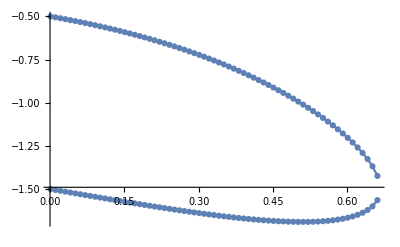

```mathematica
e0=einit;tab=Table[calc1[npair,{},α];{α,energies},{α,0.001,0.67,0.01}];
Show[{ListPlot[Map[{#[[1]],#[[2,1]]}&,tab],Joined->True,Mesh->All],ListPlot[Map[{#[[1]],#[[2,2]]}&,tab],Joined->True,Mesh->All]},PlotRange->All]
```

```mathematica
calc[n_,singly_,α_]:=Module[{},
npair=n;
e0=einit;
calc1[n,singly,α]
];
```

```mathematica
nn=4;
FullForm@calc[2,{},α=0.1]
FullForm@calc[2,{3},α]
FullForm@calc[1,{2},α]
```

-2.10617

-1.85212

-1.80212

```mathematica
nn=5;
FullForm@calc[2,{3},α=0.1]
FullForm@calc[3,{},α]
FullForm@calc[2,{},α]
```

-2.48293

-2.52628

-2.48628

```mathematica
nn=14;
FullForm@calc[7,{},α=0.1]
FullForm@calc[7,{8},α]
FullForm@calc[6,{7},α]
```

-7.10758

-7.0338

-7.01952

```mathematica
nn=15;
FullForm@calc[7,{8},α=0.1]
FullForm@calc[8,{},α]
FullForm@calc[7,{},α]
```

-7.56539

-7.58094

-7.56761

```mathematica
nn=100;
FullForm@calc[50,{},α=0.1]
FullForm@calc[50,{51},α]
FullForm@calc[49,{50},α]
```

-50.1085

-50.0977

-50.0957

```mathematica
einit:=Table[2eps[i]-10^-4(1+I),{i,npair}]; (* initial approx *)
```

```mathematica
Epairs[levels_,n_,α_]:=Module[{},
eq[ν_]:=1/(α d)+Sum[If[μ≠ν,2/(e[μ]-e[ν]),0],{μ,1,n}]==Total@Map[1/(2eps[#]-e[ν])&,levels];
eqs=Table[eq[ν],{ν,1,n}];
vars=Table[{e[i],e0[[i]]+10^-6I},{i,n}];
sol=FindRoot[eqs,vars,MaxIterations->10000];
e0=energies=sol[[All,2]];
Total[energies]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

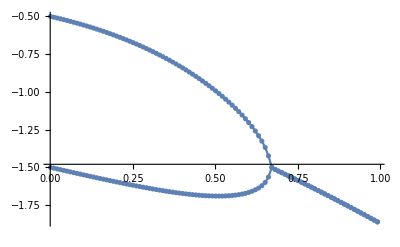

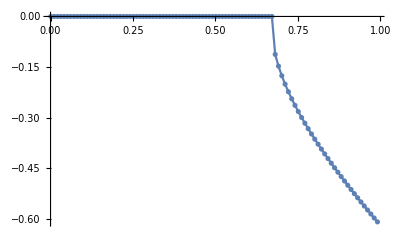

```mathematica
nn=4;npair=2;
e0=einit;tab=Table[calc1[npair,{},α];{α,energies},{α,0.001,1.0,0.01}];
Show[{ListPlot[Map[{#[[1]],Re@#[[2,1]]}&,tab],Joined->True,Mesh->All],ListPlot[Map[{#[[1]],Re@#[[2,2]]}&,tab],Joined->True,Mesh->All]},PlotRange->All]
ListPlot[Map[{#[[1]],Im@#[[2,1]]}&,tab],Joined->True,Mesh->All]
```